## Polya Urn

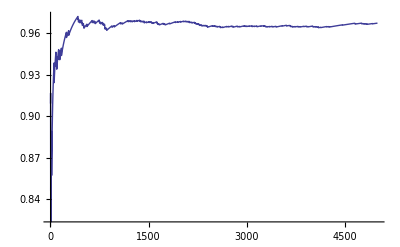

```mathematica
A={0,1,1,1,1,1,1,1,1,1};
P={};
Do[
AppendTo[A,If[RandomChoice[A]==1,1,0]];
AppendTo[P,Total[A]/Length[A]//N],
{5000}
]
ListLinePlot[P,PlotRange->All]
```

## Modiffied Polya Urn

```mathematica
G={};
Do[B={0,1};
P={};
Do[
If[RandomChoice[B]==0,B=Join[B,{0}],B=Join[B,ConstantArray[1,RandomInteger[{1,5}]]]];
AppendTo[P,Total[B]/Length[B]//N],
{3000}
]
AppendTo[G,ListLinePlot[P,PlotRange->All,PlotStyle->{Hue[RandomReal[]],Thick}]],
{10}
]
```

```mathematica
plot=Show[G,ImageSize->1000,Axes->False,Frame->True,FrameLabel->{"Iteraciones","Proporción Blancas"},AspectRatio->0.3];
```

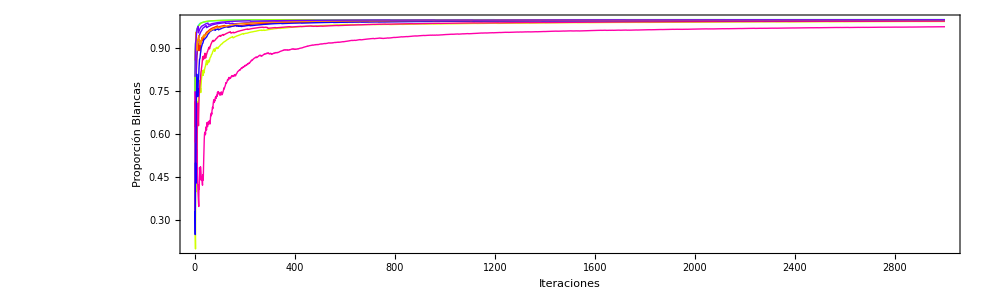

```mathematica
plot
```

```mathematica
Export["/home/polimata/Descargas/Polya10_normalmod.jpeg",plot]
```

/home/polimata/Descargas/Polya10_normalmod.jpeg

## Number of balls graph

```mathematica
G={};
Do[B={0,1};
P={};
Do[
If[RandomChoice[B]==0,B=Join[B,{0}],B=Join[B,ConstantArray[1,RandomInteger[{1,1}]]]];
AppendTo[P,Total[B]],
{3000}
]
AppendTo[G,ListPlot[P,PlotRange->All,PlotStyle->{Hue[0.0],Thin}]],
{20}
]
```

```mathematica
plot=Show[G,ImageSize->300,Axes->False,Frame->True,FrameLabel->{"Iteraciones","Proporción Blancas"},AspectRatio->0.3];
```

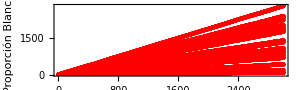

```mathematica
plot
```